{Binding Energy cs, bs, cc, bc, bb}

-0.0246512

-0.0319728

-0.0771792

-0.100745

-0.128011

{Ωc 1/2+ 2.695}

{2.67989,4.93207,{3.07937,2.95563,2.48388,2.04279}}

{0.280115}

{{-0.40578},{-0.384351}}

{Ωc^* 3/2+ 2.766}

{2.76395,5.09816,{3.08138,2.96124,2.4935,2.04279}}

{0.288747}

{{-0.339315},{-0.321396}}

{Ds 0- 1.968}

{1.9609,3.77264,{3.06053,2.90466,2.40965,2.04279}}

{0.460299,0.460299}

{Ds^* 1- 2.112}

{2.112,4.17192,{3.06818,2.92497,2.4367,2.04279}}

{0.505227,0.505227}

{{0.409371,-0.409371},{0.387753,-0.387753}}

{Ωb 1/2+ 6.046}

{6.07969,4.76783,{3.07725,2.94974,2.47414,2.04279}}

{0.59529}

{{-0.324032},{-0.30692}}

{Ωb^* 3/2+}

{6.11176,4.84453,{3.07826,2.95253,2.47872,2.04279}}

{0.604289}

{{-0.540609},{-0.51206}}

{Bs 0- 5.367}

{5.34636,3.35218,{3.05055,2.87898,2.37928,2.04279}}

{0.157975,0.157975}

{Bs^* 1- 5.415}

{5.415,3.61935,{3.05715,2.89587,2.39881,2.04279}}

{0.169315,0.169315}

{{0.380142,-0.380142},{0.360067,-0.360067}}

{ηc 0- 2.984}

{3.00164,3.15224,{3.04491,2.86484,2.36412,2.04279}}

{0.}

{Jψ 1- 3.097}

{3.097,3.54106,{3.05532,2.89114,2.39317,2.04279}}

{0.}

{{0.},{0.}}

{Bc 0- 6.275}

{6.275,2.53226,{3.02197,2.81036,2.31386,2.04279}}

{0.294459,0.294459}

{Bc^* 1-}

{6.33335,2.81449,{3.03362,2.83743,2.33737,2.04279}}

{0.324436,0.324436}

{{0.197971,-0.197971},{0.187517,-0.187517}}

{ηb 0- 9.399}

{9.39655,1.59205,{2.95594,2.6778,2.22705,2.04279}}

{0.}

{Υ 1- 9.460}

{9.46,1.79829,{2.97584,2.71427,2.2473,2.04279}}

{0.}

{{0.},{0.}}

{Ξcc 1/2+ 3.621}

{3.60392,4.42057,{3.07225,2.93601,2.45273,2.04279}}

{0.778419,0.448868}

{{0.0470245,0.345112},{0.0445412,0.326887}}

{Ξcc^* 3/2+ 1.533}

{3.71416,4.63766,{3.07546,2.9448,2.46624,2.04279}}

{0.815011,0.468068}

{{0.996903,0.0587224},{0.944257,0.0556213}}

{Ξbb 1/2+}

{10.3106,3.70724,{3.05912,2.90099,2.40505,2.04279}}

{0.287456,0.449248}

{{-0.209554,0.0404325},{-0.198487,0.0382973}}

{Ξbb^* 3/2+}

{10.3595,3.86546,{3.06244,2.9097,2.41609,2.04279}}

{0.300223,0.468103}

{{0.456882,-0.325084},{0.432755,-0.307916}}

{Mass Spectrum}

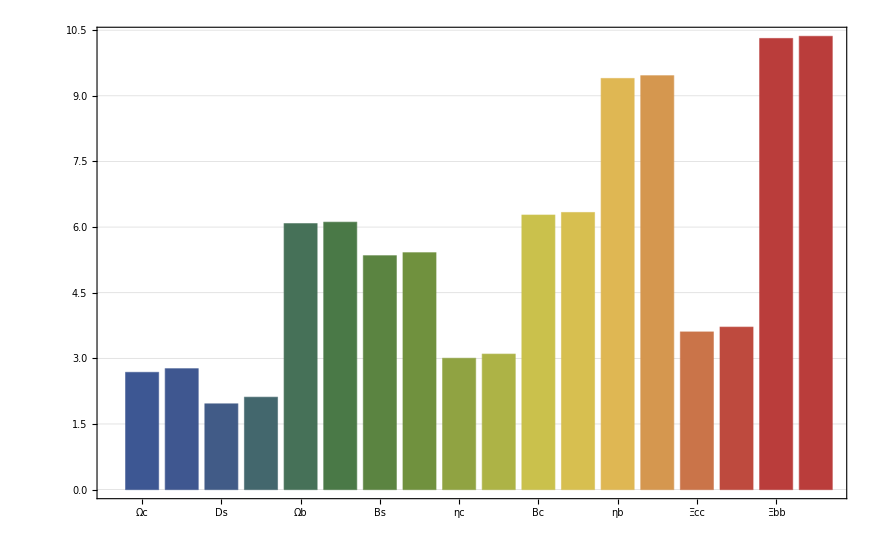

{My Error}

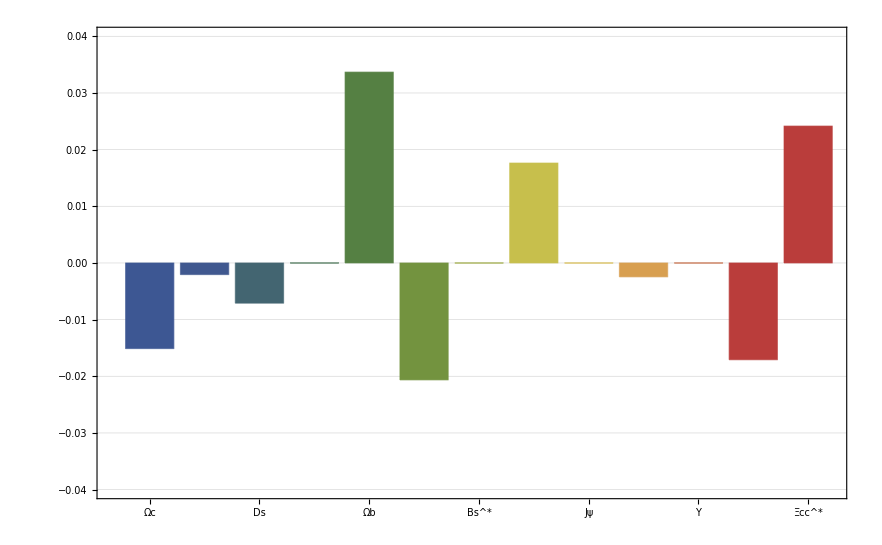

{Charge Radius}

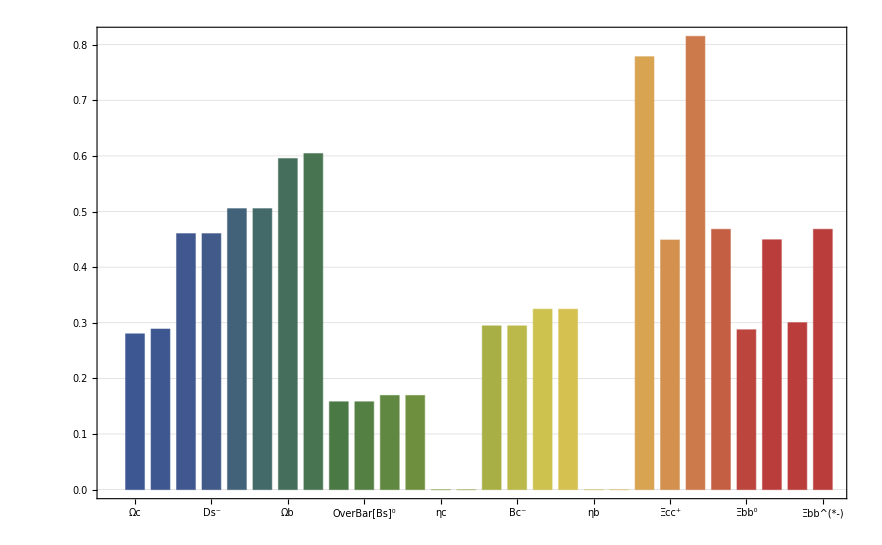

{Magnetic Moment}

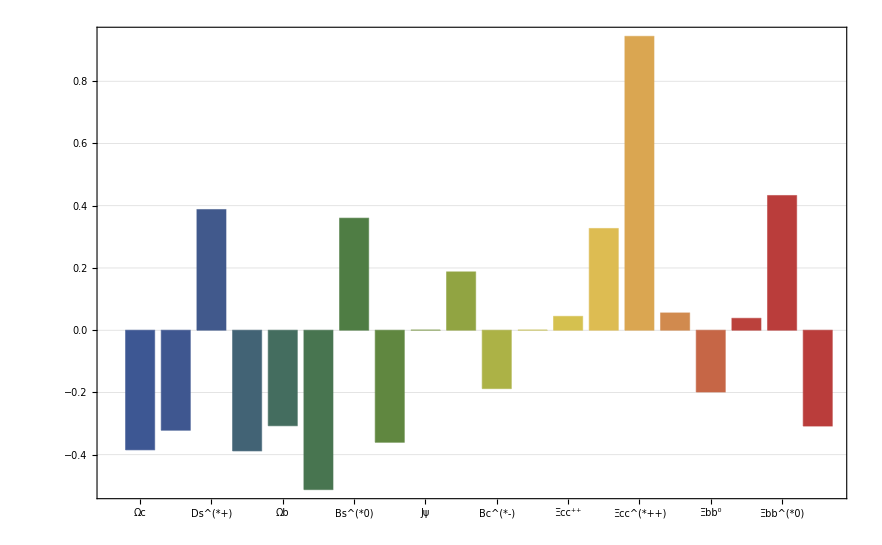

```mathematica
<<MITBagModel\MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];

{"Binding Energy cs, bs, cc, bc, bb"}
Bcs=-(First[Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},0]]-2.112)/2
Bbs=-(First[Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-5.415)/2
Bcc=-(First[Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},0]]-3.097)/2
Bbc=-(First[Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-6.275)/2
Bbb=-(First[Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-9.460)/2

{"Ωc 1/2+ 2.695"}
Ωc=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,32/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
rΩc=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},Ωc];
μΩc=MagneticMoment[{0,-1/3,4/3,0,0},{0,0,0,0,0},Ωc];
{rΩc}
{{μΩc},{μΩc/μNp}}

{"Ωc^* 3/2+ 2.766"}
SuperStar[Ωc]=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
SuperStar[rΩc]=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},SuperStar[Ωc]];
SuperStar[μΩc]=MagneticMoment[{0,1,2,0,0},{0,0,0,0,0},SuperStar[Ωc]];
{SuperStar[rΩc]}
{{SuperStar[μΩc]},{SuperStar[μΩc]/μNp}}

{"Ds 0- 1.968"}
Ds=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,16,0},{0,0,0,0},{0,0,0,0}},2Bcs]
rDsp=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},Ds];
rDsm=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},Ds];
{rDsp,rDsm}

{"Ds^* 1- 2.112"}
SuperStar[Ds]=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},2Bcs]
SuperStar[rDsp]=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},SuperStar[Ds]];
SuperStar[rDsm]=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},SuperStar[Ds]];
SuperStar[μDsp]=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},SuperStar[Ds]];
SuperStar[μDsm]=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},SuperStar[Ds]];
{SuperStar[rDsp],SuperStar[rDsm]}
{{SuperStar[μDsp],SuperStar[μDsm]},{SuperStar[μDsp]/μNp,SuperStar[μDsm]/μNp}}

{"Ωb 1/2+ 6.046"}
Ωb=Hadron[{1,0,2,0},{{0,0,32/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},2Bbs]
rΩb=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},Ωb];
μΩb=MagneticMoment[{-1/3,0,4/3,0,0},{0,0,0,0,0},Ωb];
{rΩb}
{{μΩb},{μΩb/μNp}}

{"Ωb^* 3/2+"}
SuperStar[Ωb]=Hadron[{1,0,2,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},2Bbs]
SuperStar[rΩb]=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},SuperStar[Ωb]];
SuperStar[μΩb]=MagneticMoment[{1,0,2,0,0},{0,0,0,0,0},SuperStar[Ωb]];
{SuperStar[rΩb]}
{{SuperStar[μΩb]},{SuperStar[μΩb]/μNp}}

{"Bs 0- 5.367"}
Bs=Hadron[{1,0,1,0},{{0,0,16,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs]
rBs0=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},Bs];
rBs0bar=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},Bs];
{rBs0,rBs0bar}

{"Bs^* 1- 5.415"}
SuperStar[Bs]=Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs]
SuperStar[rBs0]=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},SuperStar[Bs]];
SuperStar[rBs0bar]=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},SuperStar[Bs]];
SuperStar[μBs0]=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},SuperStar[Bs]];
SuperStar[μBs0bar]=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},SuperStar[Bs]];
{SuperStar[rBs0],SuperStar[rBs0bar]}
{{SuperStar[μBs0],SuperStar[μBs0bar]},{SuperStar[μBs0]/μNp,SuperStar[μBs0bar]/μNp}}

{"ηc 0- 2.984"}
ηc=Hadron[{0,2,0,0},{{0,0,0,0},{0,16,0,0},{0,0,0,0},{0,0,0,0}},2Bcc]
rηc=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},ηc];
{rηc}

{"Jψ 1- 3.097"}
Jψ=Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},2Bcc]
rJψ=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},Jψ];
μJψ=MagneticMoment[{0,1,0,0,0},{0,1,0,0,0},Jψ];
{rJψ}
{{μJψ},{μJψ/μNp}}

{"Bc 0- 6.275"}
Bc=Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc]
rBcp=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},Bc];
rBcm=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},Bc];
{rBcp,rBcm}

{"Bc^* 1-"}
SuperStar[Bc]=Hadron[{1,1,0,0},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc]
SuperStar[rBcp]=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},SuperStar[Bc]];
SuperStar[rBcm]=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},SuperStar[Bc]];
SuperStar[μBcp]=MagneticMoment[{0,1,0,0,0},{1,0,0,0,0},SuperStar[Bc]];
SuperStar[μBcm]=MagneticMoment[{1,0,0,0,0},{0,1,0,0,0},SuperStar[Bc]];
{SuperStar[rBcp],SuperStar[rBcm]}
{{SuperStar[μBcp],SuperStar[μBcm]},{SuperStar[μBcp]/μNp,SuperStar[μBcm]/μNp}}

{"ηb 0- 9.399"}
ηb=Hadron[{2,0,0,0},{{16,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbb]
rηb=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},ηb];
{rηb}

{"Υ 1- 9.460"}
Υ=Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbb]
rΥ=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},Υ];
μΥ=MagneticMoment[{1,0,0,0,0},{1,0,0,0,0},Υ];
{rΥ}
{{μΥ},{μΥ/μNp}}

{"Ξcc 1/2+ 3.621"}
Ξcc=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,32/3},{0,0,0,0},{0,0,0,0}},Bcc]
rΞccpp=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},Ξcc];
rΞccp=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},Ξcc];
μΞccpp=MagneticMoment[{0,4/3,0,-1/3,0},{0,0,0,0,0},Ξcc];
μΞccp=MagneticMoment[{0,4/3,0,0,-1/3},{0,0,0,0,0},Ξcc];
{rΞccpp,rΞccp}
{{μΞccpp,μΞccp},{μΞccpp/μNp,μΞccp/μNp}}

{"Ξcc^* 3/2+ 1.533"}
SuperStar[Ξcc]=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,-16/3},{0,0,0,0},{0,0,0,0}},Bcc]
SuperStar[rΞccpp]=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},SuperStar[Ξcc]];
SuperStar[rΞccp]=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},SuperStar[Ξcc]];
SuperStar[μΞccpp]=MagneticMoment[{0,2,0,1,0},{0,0,0,0,0},SuperStar[Ξcc]];
SuperStar[μΞccp]=MagneticMoment[{0,2,0,0,1},{0,0,0,0,0},SuperStar[Ξcc]];
{SuperStar[rΞccpp],SuperStar[rΞccp]}
{{SuperStar[μΞccpp],SuperStar[μΞccp]},{SuperStar[μΞccpp]/μNp,SuperStar[μΞccp]/μNp}}

{"Ξbb 1/2+"}
Ξbb=Hadron[{2,0,0,1},{{-8/3,0,0,32/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Bbb]
rΞbb0=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},Ξbb];
rΞbbm=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},Ξbb];
μΞbb0=MagneticMoment[{4/3,0,0,-1/3,0},{0,0,0,0,0},Ξbb];
μΞbbm=MagneticMoment[{4/3,0,0,0,-1/3},{0,0,0,0,0},Ξbb];
{rΞbb0,rΞbbm}
{{μΞbb0,μΞbbm},{μΞbb0/μNp,μΞbbm/μNp}}

{"Ξbb^* 3/2+"}
SuperStar[Ξbb]=Hadron[{2,0,0,1},{{-8/3,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Bbb]
SuperStar[rΞbb0]=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},SuperStar[Ξbb]];
SuperStar[rΞbbm]=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},SuperStar[Ξbb]];
SuperStar[μΞbb0]=MagneticMoment[{2,0,0,1,0},{0,0,0,0,0},SuperStar[Ξbb]];
SuperStar[μΞbbm]=MagneticMoment[{2,0,0,0,1},{0,0,0,0,0},SuperStar[Ξbb]];
{SuperStar[rΞbb0],SuperStar[rΞbbm]}
{{SuperStar[μΞbb0],SuperStar[μΞbbm]},{SuperStar[μΞbb0]/μNp,SuperStar[μΞbbm]/μNp}}


{"Mass Spectrum"}
BarChart[{First[Ωc],First[SuperStar[Ωc]],First[Ds],First[SuperStar[Ds]],First[Ωb],First[SuperStar[Ωb]],First[Bs],First[SuperStar[Bs]],First[ηc],First[Jψ],First[Bc],First[SuperStar[Bc]],First[ηb],First[Υ],First[Ξcc],First[SuperStar[Ξcc]],First[Ξbb],First[SuperStar[Ξbb]]},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds","Ds^*","Ωb","Ωb^*","Bs","Bs^*","ηc","Jψ","Bc","Bc^*","ηb","Υ","Ξcc","Ξcc^*","Ξbb","Ξbb^*"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{
(First[Ωc]-2.695),
(First[SuperStar[Ωc]]-2.766),
(First[Ds]-1.968),
(First[SuperStar[Ds]]-2.112),
(First[Ωb]-6.046),
(First[Bs]-5.367),
(First[SuperStar[Bs]]-5.415),
(First[ηc]-2.984),
(First[Jψ]-3.097),
(First[ηb]-9.399),
(First[Υ]-9.460),
(First[Ξcc]-3.621),
(First[SuperStar[Ξcc]]-3.690)},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds","Ds^*","Ωb","Bs","Bs^*","ηc","Jψ","ηb","Υ","Ξcc","Ξcc^*"},ChartStyle->"DarkRainbow",PlotRange->{-0.04,0.04},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΩc,SuperStar[rΩc],rDsp,rDsm,SuperStar[rDsp],SuperStar[rDsm],rΩb,SuperStar[rΩb],rBs0,rBs0bar,SuperStar[rBs0],SuperStar[rBs0bar],rηc,rJψ,rBcp,rBcm,SuperStar[rBcp],SuperStar[rBcm],rηb,rΥ,rΞccpp,rΞccp,SuperStar[rΞccpp],SuperStar[rΞccp],rΞbb0,rΞbbm,SuperStar[rΞbb0],SuperStar[rΞbbm]},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds^+","Ds^-","Ds^(*+)","Ds^(*-)","Ωb","Ωb^*","Bs^0","OverBar[Bs]^0","Bs^(*0)","OverBar[Bs]^(*0)","ηc","Jψ","Bc^+","Bc^-","Bc^(*+)","Bc^(*-)","ηb","Υ","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΩc/μNp,SuperStar[μΩc]/μNp,SuperStar[μDsp]/μNp,SuperStar[μDsm]/μNp,μΩb/μNp,SuperStar[μΩb]/μNp,SuperStar[μBs0]/μNp,SuperStar[μBs0bar]/μNp,μJψ/μNp,SuperStar[μBcp]/μNp,SuperStar[μBcm]/μNp,μΥ/μNp,μΞccpp/μNp,μΞccp/μNp,SuperStar[μΞccpp]/μNp,SuperStar[μΞccp]/μNp,μΞbb0/μNp,μΞbbm/μNp,SuperStar[μΞbb0]/μNp,SuperStar[μΞbbm]/μNp},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds^(*+)","Ds^(*-)","Ωb","Ωb^*","Bs^(*0)","OverBar[Bs]^(*0)","Jψ","Bc^(*+)","Bc^(*-)","Υ","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```